```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

## Preparation

```mathematica
eqs=<<eqs.m;
bcsr1=<<bcsr1.m;
bcsr0=<<bcsr0.m;
jacobi=<<jacobi.m;
jacobir1=<<jacobir1.m;
jacobir0=<<jacobir0.m;
check=<<check.m;
(*Parameters*)
L=1;Lr=1.0;Lx=N[2π];
A0=1.5;k0=2;
mu=1.4;t=0.043;T=t mu;
zh=1/6 (4 π T+√(16 π^2 T^2+6 mu^2));
Nr=30;Nx=60;Nrx=Nr*Nx;
Eye=IdentityMatrix[Nrx];Zero=ConstantArray[0,{Nrx,Nrx}];
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
dr=cheb[Nr,Lr];
drs[0]=IdentityMatrix[Nr];drs[1]=dr;drs[2]=dr.dr;
gridr=0.5(chebp[Nr]+1);rr=gridr⊗ConstantArray[1,Nx];R=Flatten[rr];
(*boundary index of holographic coordinate*)
r1=Flatten[Position[R,n_/;n==gridr⟦1⟧]];r0=Flatten[Position[R,n_/;n==gridr⟦-1⟧]];
rb=Join[r0,r1];
(*Fourier谱求导矩阵生成函数*)
fourier[n_,l_]:=π/l Table[If[i==j,0,(-1)^(i-j)If[Mod[n,2]==0,Cot[(π*(i-j))/n],Csc[(π*(i-j))/n]]],{i,1,n},{j,1,n}];
dx=fourier[Nx,Lx];
dxs[0]=IdentityMatrix[Nx];dxs[1]=dx;dxs[2]=dx.dx;
gridx=Lx/Nx Range[0,Nx-1];xx=ConstantArray[1,Nr]⊗gridx;X=Flatten[xx];
(*derivative matrix after vectorization*)
Do[If[i+j≤ 2,ds[i,j]=KroneckerProduct[drs[i],dxs[j]]],{i,0,2},{j,0,2}];
```

## Solution

### initialization

```mathematica
last=0;
If[last==1,
(*last outcome*)
q[1]=s[Q1]=<<Q1.m;
q[2]=s[Q2]=<<Q2.m;
q[3]=s[Q3]=<<Q3.m;
q[4]=s[Q4]=<<Q4.m;
q[5]=s[Q5]=<<Q5.m;
q[6]=s[Q6]=<<Q6.m;
q[7]=s[Q7]=<<Q7.m;,
(*seed*)
q[1]=s[Q1]=ConstantArray[1,Nrx];
q[2]=s[Q2]=ConstantArray[1,Nrx];
q[3]=s[Q3]=ConstantArray[0,Nrx];
q[4]=s[Q4]=ConstantArray[1,Nrx];
q[5]=s[Q5]=ConstantArray[1,Nrx];
q[6]=s[Q6]=0.1Cos[k0 X];
q[7]=s[Q7]=ConstantArray[1,Nrx];]
(*q[1]=s[Q1]=ReadList["Q1.m"]⟦j⟧;
q[2]=s[Q2]=ReadList["Q2.m"]⟦j⟧;
q[3]=s[Q3]=ReadList["Q3.m"]⟦j⟧;
q[4]=s[Q4]=ReadList["Q4.m"]⟦j⟧;
q[5]=s[Q5]=ReadList["Q5.m"]⟦j⟧;
q[6]=s[Q6]=ReadList["Q6.m"]⟦j⟧;
q[7]=s[Q7]=ReadList["Q7.m"]⟦j⟧;*)
(*(*reshape*)
Do[req[i]=ArrayReshape[q[i],{Nr,Nx}],{i,7}];
(*interpolate function*)
Do[interfunq[i]=ListInterpolation[Append[req[i]ᵀ,req[i]⟦;;,1⟧]ᵀ,{gridr,Append[gridx,0.5Lx]}],{i,7}];*)
```

### interpolation

```mathematica
(*resample*)
Do[q[k]=Flatten[Table[interfunq[k][gridr⟦i⟧,gridx⟦j⟧],{i,Nr},{j,Nx}]],{k,7}];
{s[Q1],s[Q2],s[Q3],s[Q4],s[Q5],s[Q6],s[Q7]}={q[1],q[2],q[3],q[4],q[5],q[6],q[7]};
```

### iteration

```mathematica
seed=Join[q[1],q[2],q[3],q[4],q[5],q[6],q[7]];length=Length[seed];
eps=10^-6;k=0;kmax=12;done=1;rmssollist={};
Monitor[While[done==1&&k<kmax,
diseqs=eqs/.{Derivative[i_,j_][h_][r,x]->ds[i,j].s[h],h_[r,x]->s[h],r->R};
disbcsr1=bcsr1/.{Derivative[i_,j_][h_][r,x]:>(ds[i,j]⟦r1⟧).s[h],h_[r,x]:>s[h]⟦r1⟧,x:>X⟦r1⟧};
disbcsr0=bcsr0/.{Derivative[i_,j_][h_][r,x]:>(ds[i,j]⟦r0⟧).s[h],h_[r,x]:>s[h]⟦r0⟧};
diseqs⟦;;,r1⟧=disbcsr1;
diseqs⟦;;,r0⟧=disbcsr0;
b=-Flatten[diseqs];
	
J=jacobi/.{Derivative[i_,j_][h_][r,x]->ds[i,j].s[h],h_[r,x]->s[h],Subscript[d, i_,j_]->ds[i,j],eye->Eye,zero->Zero,r->R};
Jr1=jacobir1/.{Derivative[i_,j_][h_][r,x]:> (ds[i,j]⟦r1⟧).s[h],h_[r,x]:> s[h]⟦r1⟧,Subscript[d, i_,j_]:> ds[i,j]⟦r1⟧,eye:> Eye⟦r1⟧,zero:> Zero⟦r1⟧};
Jr0=jacobir0/.{Derivative[i_,j_][h_][r,x]:> (ds[i,j]⟦r0⟧).s[h],h_[r,x]:> s[h]⟦r0⟧,Subscript[d, i_,j_]:> ds[i,j]⟦r0⟧,eye:> Eye⟦r0⟧,zero:> Zero⟦r0⟧};
J⟦;;,;;,r1⟧=Jr1;
J⟦;;,;;,r0⟧=Jr0;
J=ArrayFlatten[J];
sol=LinearSolve[J,b];
seed+=sol;k++;
reseed=ArrayReshape[seed,{7,Nrx}];
q[1]=s[Q1]=reseed⟦1⟧;
q[2]=s[Q2]=reseed⟦2⟧;
q[3]=s[Q3]=reseed⟦3⟧;
q[4]=s[Q4]=reseed⟦4⟧;
q[5]=s[Q5]=reseed⟦5⟧;
q[6]=s[Q6]=reseed⟦6⟧;
q[7]=s[Q7]=reseed⟦7⟧;
rmssol=√(Total[sol^2]/length);
AppendTo[rmssollist,rmssol];
If[rmssol≤eps,done=0;Print[rmssollist]];
],rmssollist];
```

{0.162546,0.0179061,0.0010169,0.0000147349,1.73792×10^-9}

### data and visualization

-Graphics3D-

-Graphics3D-

-Graphics3D-

«4 more identical outputs»

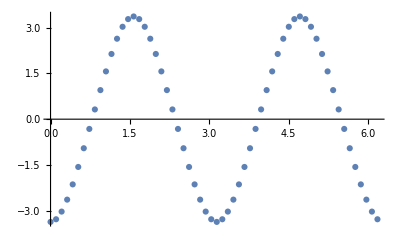

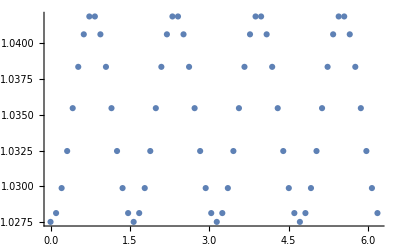

```mathematica
Do[solq[i]=ArrayReshape[q[i],{Nr,Nx}],{i,7}];
orderp=-zh/2(dr⟦1⟧.solq[6]);
density=mu zh(1+1/2(dr⟦1⟧.solq[7]));
ListPlot3D[Flatten[Table[{gridr⟦i⟧,gridx⟦j⟧,solq[6]⟦i,j⟧},{i,Nr},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridr⟦i⟧,gridx⟦j⟧,solq[7]⟦i,j⟧},{i,Nr},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridr⟦i⟧,gridx⟦j⟧,solq[1]⟦i,j⟧},{i,Nr},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridr⟦i⟧,gridx⟦j⟧,solq[2]⟦i,j⟧},{i,Nr},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridr⟦i⟧,gridx⟦j⟧,solq[3]⟦i,j⟧},{i,Nr},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridr⟦i⟧,gridx⟦j⟧,solq[4]⟦i,j⟧},{i,Nr},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridr⟦i⟧,gridx⟦j⟧,solq[5]⟦i,j⟧},{i,Nr},{j,Nx}],1],PlotRange->All]
ListPlot[Table[{gridx⟦i⟧,orderp⟦i⟧},{i,1,Nx}],PlotRange->All]
ListPlot[Table[{gridx⟦i⟧,density⟦i⟧},{i,1,Nx}],PlotRange->All]
```

### check DeTurck vector

```mathematica
subcheck=check/.{Derivative[i_,j_][h_][r,x]-> ds[i,j].s[h],h_[r,x]->s[h],r->R};
subcheck⟦rb⟧=0;
rmsxi=√(Total[subcheck^2]/Length[subcheck])
```

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

1.03959×10^-9